## Constants

```mathematica
c= 3*10^8;
h = 6.63*10^-34;
γ = 2π*6*10^6;
mRb = 87*1.66*10^-27;
ω1064 = 2π*c/(1064.*10^-9);
ω532 = 2π*c/(532*10^-9);
ωD1 = 2π*c/(780.*10^-9);
ωD2 = 2π*c/(795.*10^-9);
ER = h^2/(2*mRb*(1064*10^-9)^2);
ERG = h^2/(2*mRb*(532*10^-9)^2);
```

## Parameters

Note : Always working in real units

### 1/e^2 radii

```mathematica
wODTA=54*10^-6;(*taking 2.085 as reference*)
(*wODTA=48*10^-6;(*taking 2.25 as reference*)*)
wODTB=50*10^-6;
(*wVL = 190*10^-6;*old*)
wVL = 85*10^-6;(*after feb 27*)
w1064=85*10^-6;
w532=140*10^-6;
```

```mathematica
{{□, ODTA, ODTB, VL, 1064, 532}, {inferred radius (μm), 54, ?, ?, 85, ?}, {measured radius (μm), 43, 50, 85, ?, 140}, {reference NB# and page#, #20 
p109, □, #20
p75, □, #22
p112}}
```

{{□,ODTA,ODTB,VL,1064,532},{inferred radius μm,54,Null,Null,85,Null},{measured radius μm,43,50,85,Null,140},{and NB# page# reference,p109 #20,□,p75 #20,□,p112 #22}}

### Calibrations

```mathematica
V0ODTA=1.75;
```

### Vertical lattice

```mathematica
PVL=80.6*10^(-0.08/0.4)*10^-3;
η=Sqrt[0.76];(* Electric field ratio: √(Power Ratio) *)
```

```mathematica
PVL = 0.23;
wVL =  190*10^-6;
```

## Trap frequency

### ODTs

```mathematica
α=(3*π*c^2*γ)/(2*ωD1^3)*1/3(1./(ωD1-ω1064)+1/(ωD1+ω1064))+(3*π*c^2*γ)/(2*ωD2^3)*2/3(1./(ωD2-ω1064)+1/(ωD2+ω1064));
V0[P_,w_]:=(α*2P)/(π*w^2)
```

```mathematica
VODTA[v_]:=10^((v-V0ODTA)/0.4)*10^-3;
```

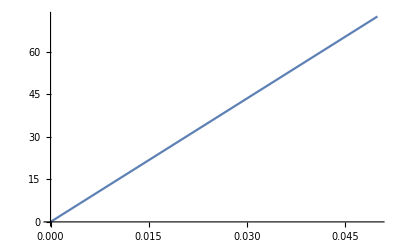

```mathematica
Plot[V0[P,wODTA]*2/h/1000,{P,0,0.05}]
```

```mathematica
ωODT[P_]:=((4*V0[P,wODTA])/(mRb*wODTA^2))/(2π)^2
```

```mathematica
ωODTx[P_]:=1/2*ωODT[P]
ωODTy[P_]:=3/2*ωODT[P]
ωODTz[P_]:=2*ωODT[P]
```

```mathematica
ODTfinal = 2.085;
ωODTx[VODTA[ODTfinal]]^0.5
ωODTy[VODTA[ODTfinal]]^0.5
ωODTz[VODTA[ODTfinal]]^0.5
```

19.9482

34.5513

39.8964

```mathematica
ODTfinal = 2.35;
ωbarODT = (ωODTx[VODTA[ODTfinal]]^0.5*ωODTy[VODTA[ODTfinal]]^0.5*ωODTy[VODTA[ODTfinal]]^0.5)^(1/3)
```

61.6871

### ODTs + VL

This formula is from Sebastian Will’s thesis, (2.68)

```mathematica
(1-1/4)^0.5
```

0.866025

```mathematica
PVL=0.1
η=0.87^2
```

0.1

0.7569

```mathematica
ωVL[P_]:=(1/(mRb wVL^2)((η+1)^2*4*V0[P,wVL]-2(ER*η*4*V0[P,wVL])^0.5))/(2π)^2;
```

The trap frequency at the set power is

```mathematica
(ωVL[PVL])^0.5
```

13.9422

The trap depth at the expected power is

```mathematica
η*4V0[PVL,wVL]/h
```

17738.5

The VLx2 + Comp trap frequencies are

```mathematica
√(ωODTx[VODTA[2.2]]+ωVL[PVL])
√(ωODTy[VODTA[2.085]]+ωVL[PVL])
```

24.3375

37.2583

```mathematica
58.5/65
```

0.9

#### Other Calc

```mathematica
((ωODTx[VODTA[ODTfinal]])+(ωVL[PVL]))^0.5
```

24.3375

```mathematica
((ωODTy[VODTA[ODTfinal]])+(ωVL[PVL]))^0.5
```

37.2583

### ODTs + VL + 1064 lattice

#### with extra B2

```mathematica
ωB2[V_]:=((4*V)/(mRb*w1064^2))/(2π)^2
```

```mathematica
ωIR [VIR_]:= ((2*VIR)/(mRb*w1064^2)-(√3)/(√2*mRb*w1064^2)*(ER*VIR)^0.5)/(2π)^2
```

```mathematica
ωIRz[VIR_]:= ((4*VIR)/(3mRb*w1064^2)-(√6)/(mRb*w1064^2)*(ER*VIR)^0.5)/(2π)^2
```

```mathematica
ODTfinal=2.085;
```

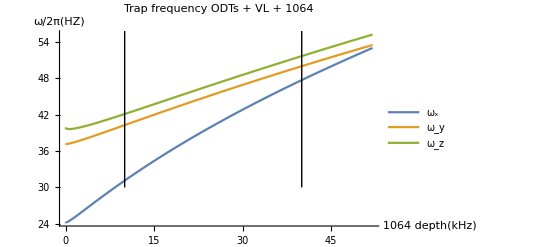

```mathematica
lineIR1=Line[{{10,30},{10,90}}];
lineIR2=Line[{{40,30},{40,90}}];
Plot[{(ωODTx[VODTA[ODTfinal]]+(ωVL[PVL])+(ωIR[V*h*1000])+(ωB2[2*V*h*1000/9]))^0.5,((ωODTy[VODTA[ODTfinal]])+(ωVL[PVL])+(ωIR[V*h*1000]))^0.5,(ωODTz[VODTA[ODTfinal]]+(ωIRz[V*h*1000])+(ωB2[2*V*h*1000/9]))^0.5},{V,0,52},PlotLegends->{"ω_x","ω_y","ω_z"},Epilog->{Directive[lineStyle],lineIR1,lineIR2},AxesLabel->{"1064 depth(kHz)","ω/2π(HZ)"},PlotLabel->"Trap frequency ODTs + VL + 1064"]
```

```mathematica
ωbarIR[VODT_,V1064_] := ((ωODTx[VODTA[VODT]]+(ωVL[PVL])+(ωIR[V1064*h*1000])+(ωB2[2*V1064*h*1000/9]))^0.5*(ωODTy[VODTA[VODT]]+(ωVL[PVL])+(ωIR[V1064*h*1000]))^0.5*(ωODTz[VODTA[VODT]]+(ωIRz[V1064*h*1000])+(ωB2[2*V1064*h*1000/9]))^0.5)^(1/3)
```

```mathematica
ODTfinal=2.085;
V1064=40;
```

```mathematica
ωbarIR[2.09,V1064]
```

53.373

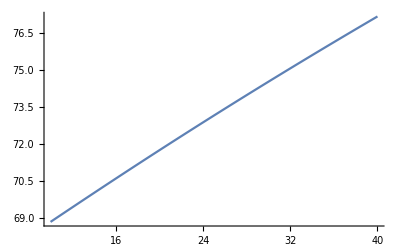

```mathematica
Plot[ωbarIR[2.35,V],{V,10,40}]
```

#### ideal 1064 lattice

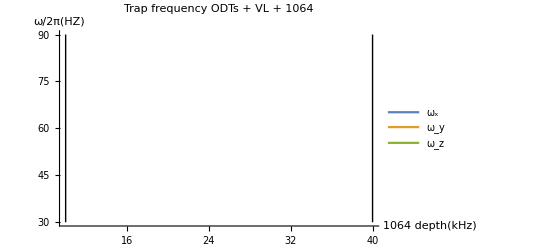

```mathematica
lineIR1=Line[{{10,30},{10,90}}];
lineIR2=Line[{{40,30},{40,90}}];
Plot[{(ωODTx[ODTA[ODTfinal]]+(ωVL[PVL])+(ωIR[V*h*1000]))^0.5,((ωODTy[ODTA[ODTfinal]])+(ωVL[PVL])+(ωIR[V*h*1000]))^0.5,(ωODTz[ODTA[ODTfinal]]+(ωIRz[V*h*1000]))^0.5},{V,0,52},PlotLegends->{"ω_x","ω_y","ω_z"},Epilog->{Directive[lineStyle],lineIR1,lineIR2},AxesLabel->{"1064 depth(kHz)","ω/2π(HZ)"},PlotLabel->"Trap frequency ODTs + VL + 1064"]
```

### ODTs + VL + 532 lattice

```mathematica
α532=(3*π*c^2*γ)/(2*ωD1^3)*1/3(1./(ωD1-ω532)+1/(ωD1+ω532))+(3*π*c^2*γ)/(2*ωD2^3)*2/3(1./(ωD2-ω532)+1/(ωD2+ω532));
```

```mathematica
V0532[P_,w_]:=(α532*2P)/(π*w^2)
```

```mathematica
9/2*V0532[(230*290*340)^(1/3)/1000,w532]/(6.63*10^-34)/1000
```

-51.0994

```mathematica
ωGreen [VGreen_]:= -((√3)/(√2*mRb*w532^2)*(ERG*VGreen)^0.5)/(2π)^2
ωGreenz[VGreen_]:=-( (√6)/(mRb*w532^2)*(2*ERG*VGreen)^0.5)/(2π)^2
```

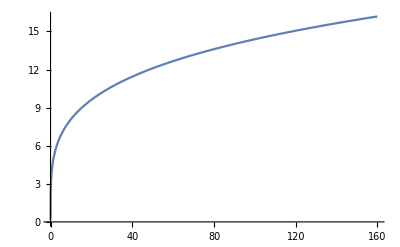

```mathematica
Plot[Abs[ωGreen [V*h*1000]]^0.5,{V,0,160} ]
```

```mathematica
ODTfinal = 2.25;
```

```mathematica
Plot[{(ωODTx[VODTA[ODTfinal]]+ωVL[PVL]+ωGreen[V*h*1000])^0.5,((ωODTy[VODTA[ODTfinal]])+ωVL[PVL]+ωGreen[V*h*1000])^0.5,((ωODTz[VODTA[ODTfinal]])+ωGreenz[V*h*1000])^0.5},{V,0,160},PlotLegends->{"ω_x","ω_y","ω_z"},Epilog->{Directive[lineStyle],lineG3,lineG4},AxesLabel->{"532 depth(kHz)","ω/2π(HZ)"},PlotLabel->"Trap frequency comp. ODTs + VL + 532"]
```

-Graphics-

```mathematica
ωbarG[VODT_,V532_] := ((ωODTx[VODTA[VODT]]+ωVL[PVL]+ωGreen[V532*h*1000])^0.5*((ωODTy[VODTA[VODT]])+ωVL[PVL]+ωGreen[V532*h*1000])^0.5*((ωODTz[VODTA[VODT]])+ωGreenz[V532*h*1000])^0.5)^(1/3)
```

```mathematica
PVL=0.6; (*from measurement*)
η=0.3;
```

```mathematica
ωbarG[ODTfinal,120]
```

51.5093

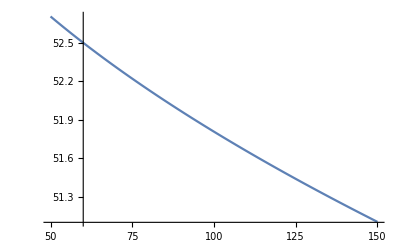

```mathematica
Plot[ωbarG[ODTfinal,V],{V,50,150}]
```

## Thomas-Fermi radius

```mathematica
mRb = 87*1.66*10^-27;
hbar = 6.63*10^-34/(2π);
Num = 5*10^4;
aho[ω_] := (hbar/(mRb*ω))^0.5;
μ[ωbar_,ω_] := (hbar*ωbar)/2*((15*Num*100*0.52*10^-10)/aho[ω])^(2/5);
RTF[ωbar_,ω_]:=((2*μ[ωbar,ω])/(mRb*ω^2))^0.5*10^6(*in microns*)
```